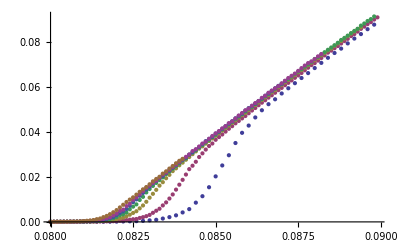

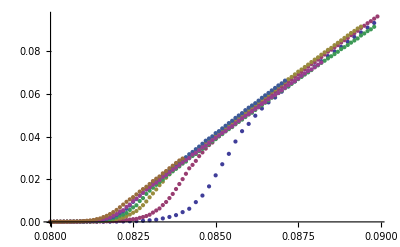

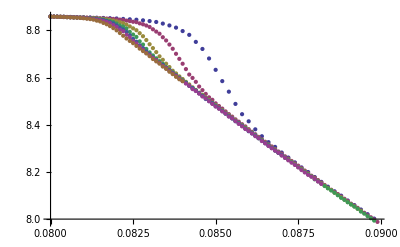

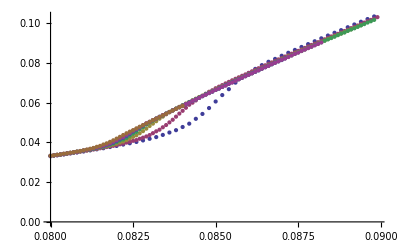

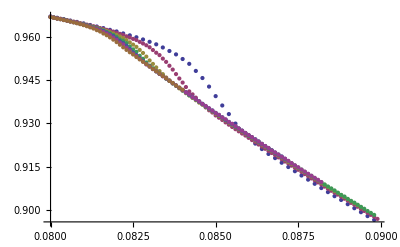

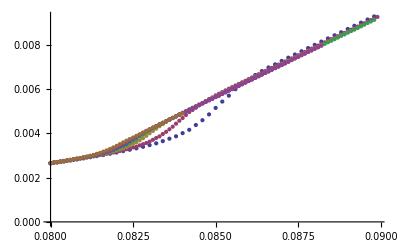

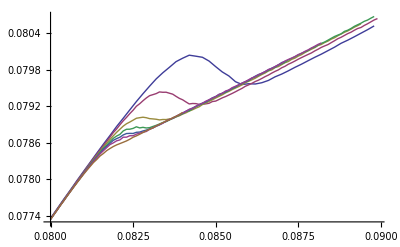

```mathematica
v="9";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l5k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l5k-v"<>v<>"-p0.1.txt",{Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l10k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l10k-v"<>v<>"-p0.1.txt",{Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l20k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l20k-v"<>v<>"-p0.1.txt",{Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l30k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l30k-v"<>v<>"-p0.1.txt",{Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l40k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l40k-v"<>v<>"-p0.1.txt",{Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l50k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l50k-v"<>v<>"-p0.1.txt",{Number,Number}];
g100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapD-l100k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/velD-l100k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/AveVel-l100k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
ncb100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarB-l100k-v"<>v<>"-p0.1.txt",{Number,Number}];
ncf100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/NumCarF-l100k-v"<>v<>"-p0.1.txt",{Number,Number}];
ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v9=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v9=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v9=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
ncf5v9=Table[{ncf5k1[[All,1]][[j]],ncf5k1[[All,2]][[j]]/(5000.*ncf5k1[[All,1]][[j]])},{j,1,Length[ncf5k1]}];
ncb5v9=Table[{ncb5k1[[All,1]][[j]],ncb5k1[[All,2]][[j]]/(5000.*ncb5k1[[All,1]][[j]])},{j,1,Length[ncb5k1]}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v9=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v9=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
ncf10v9=Table[{ncf10k1[[All,1]][[j]],ncf10k1[[All,2]][[j]]/(10000.*ncf10k1[[All,1]][[j]])},{j,1,Length[ncf10k1]}];
ncb10v9=Table[{ncb10k1[[All,1]][[j]],ncb10k1[[All,2]][[j]]/(10000.*ncb10k1[[All,1]][[j]])},{j,1,Length[ncb10k1]}];
gap20v9=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v9=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v9=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
ncf20v9=Table[{ncf20k1[[All,1]][[j]],ncf20k1[[All,2]][[j]]/(20000.*ncf20k1[[All,1]][[j]])},{j,1,Length[ncf20k1]}];
ncb20v9=Table[{ncb20k1[[All,1]][[j]],ncb20k1[[All,2]][[j]]/(20000.*ncb20k1[[All,1]][[j]])},{j,1,Length[ncb20k1]}];
gap30v9=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v9=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v9=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
ncf30v9=Table[{ncf30k1[[All,1]][[j]],ncf30k1[[All,2]][[j]]/(30000.*ncf30k1[[All,1]][[j]])},{j,1,Length[ncf30k1]}];
ncb30v9=Table[{ncb30k1[[All,1]][[j]],ncb30k1[[All,2]][[j]]/(30000.*ncb30k1[[All,1]][[j]])},{j,1,Length[ncb30k1]}];
gap40v9=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
vel40v9=Table[{v40k1[[All,1]][[j]],Sum[v40k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v40k1]}];
avel40v9=Table[{av40k1[[All,1]][[j]],av40k1[[All,2]][[j]]},{j,1,Length[av40k1]}];
ncf40v9=Table[{ncf40k1[[All,1]][[j]],ncf40k1[[All,2]][[j]]/(40000.*ncf40k1[[All,1]][[j]])},{j,1,Length[ncf40k1]}];
ncb40v9=Table[{ncb40k1[[All,1]][[j]],ncb40k1[[All,2]][[j]]/(40000.*ncb40k1[[All,1]][[j]])},{j,1,Length[ncb40k1]}];
gap50v9=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v9=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v9=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
ncf50v9=Table[{ncf50k1[[All,1]][[j]],ncf50k1[[All,2]][[j]]/(50000.*ncf50k1[[All,1]][[j]])},{j,1,Length[ncf50k1]}];
ncb50v9=Table[{ncb50k1[[All,1]][[j]],ncb50k1[[All,2]][[j]]/(50000.*ncb50k1[[All,1]][[j]])},{j,1,Length[ncb50k1]}];
gap100v9=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g100k1]}];
vel100v9=Table[{v100k1[[All,1]][[j]],Sum[v100k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v100k1]}];
avel100v9=Table[{av100k1[[All,1]][[j]],av100k1[[All,2]][[j]]},{j,1,Length[av100k1]}];
ncf100v9=Table[{ncf100k1[[All,1]][[j]],ncf100k1[[All,2]][[j]]/(100000.*ncf100k1[[All,1]][[j]])},{j,1,Length[ncf100k1]}];
ncb100v9=Table[{ncb100k1[[All,1]][[j]],ncb100k1[[All,2]][[j]]/(100000.*ncb100k1[[All,1]][[j]])},{j,1,Length[ncb100k1]}];


ncfn5v9=Table[{ncf5k1[[All,1]][[j]],ncf5k1[[All,2]][[j]]/(5000.)},{j,1,Length[ncf5k1]}];
ncbn5v9=Table[{ncb5k1[[All,1]][[j]],ncb5k1[[All,2]][[j]]/(5000.)},{j,1,Length[ncf5k1]}];
ncfn10v9=Table[{ncf10k1[[All,1]][[j]],ncf10k1[[All,2]][[j]]/(10000.)},{j,1,Length[ncf10k1]}];
ncbn10v9=Table[{ncb10k1[[All,1]][[j]],ncb10k1[[All,2]][[j]]/(10000.)},{j,1,Length[ncf10k1]}];
ncfn20v9=Table[{ncf20k1[[All,1]][[j]],ncf20k1[[All,2]][[j]]/(20000.)},{j,1,Length[ncf20k1]}];
ncbn20v9=Table[{ncb20k1[[All,1]][[j]],ncb20k1[[All,2]][[j]]/(20000.)},{j,1,Length[ncf20k1]}];
ncfn30v9=Table[{ncf30k1[[All,1]][[j]],ncf30k1[[All,2]][[j]]/(30000.)},{j,1,Length[ncf30k1]}];
ncbn30v9=Table[{ncb30k1[[All,1]][[j]],ncb30k1[[All,2]][[j]]/(30000.)},{j,1,Length[ncf30k1]}];
ncfn40v9=Table[{ncf40k1[[All,1]][[j]],ncf40k1[[All,2]][[j]]/(40000.)},{j,1,Length[ncf40k1]}];
ncbn40v9=Table[{ncb40k1[[All,1]][[j]],ncb40k1[[All,2]][[j]]/(40000.)},{j,1,Length[ncf40k1]}];
ncfn50v9=Table[{ncf50k1[[All,1]][[j]],ncf50k1[[All,2]][[j]]/(50000.)},{j,1,Length[ncf50k1]}];
ncbn50v9=Table[{ncb50k1[[All,1]][[j]],ncb50k1[[All,2]][[j]]/(50000.)},{j,1,Length[ncf50k1]}];
ncfn100v9=Table[{ncf100k1[[All,1]][[j]],ncf100k1[[All,2]][[j]]/(100000.)},{j,1,Length[ncf100k1]}];
ncbn100v9=Table[{ncb100k1[[All,1]][[j]],ncb100k1[[All,2]][[j]]/(100000.)},{j,1,Length[ncf100k1]}];

ListPlot[{gap5v9,gap10v9,gap20v9,gap30v9,gap40v9,gap50v9,gap100v9}]
ListPlot[{vel5v9,vel10v9,vel20v9,gap30v9,vel40v9,gap50v9,vel100v9}]
ListPlot[{avel5v9,avel10v9,avel20v9,avel30v9,avel40v9,avel50v9,avel100v9}]
ListPlot[{ncb5v9,ncb10v9,ncb20v9,ncb30v9,ncb40v9,ncb50v9,ncb100v9}]
ListPlot[{ncf5v9,ncf10v9,ncf20v9,ncf30v9,ncf40v9,ncf50v9,ncf100v9}]
ListPlot[{ncbn5v9,ncbn10v9,ncbn20v9,ncbn30v9,ncbn40v9,ncbn50v9,ncbn100v9}]
ListLinePlot[{ncfn5v9,ncfn10v9,ncfn20v9,ncfn30v9,ncfn40v9,ncfn50v9,ncfn100v9}]
```

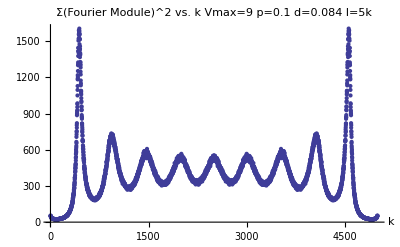

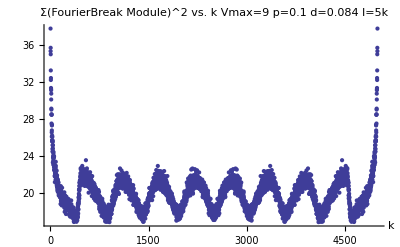

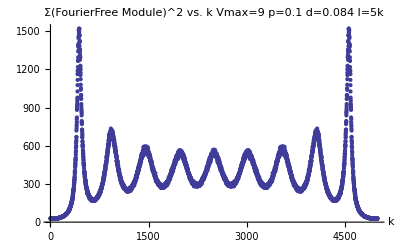

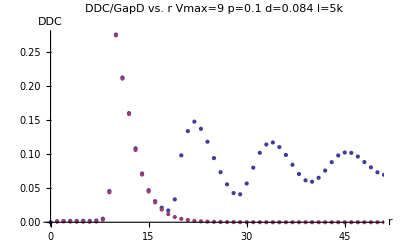

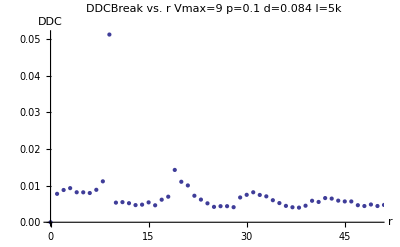

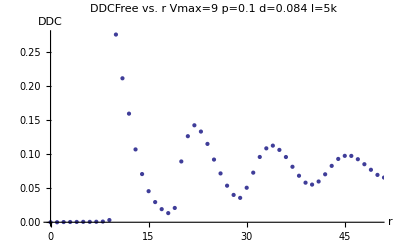

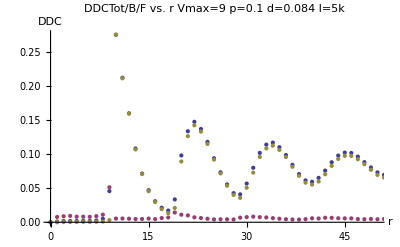

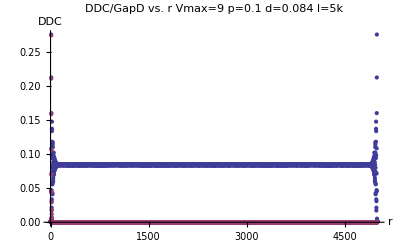

```mathematica
d="0.084";
l="5";
v="9";
p="0.1";
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddc=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/DDC-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
fourierb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1DBreak-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddcb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/DDCB-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
fourierf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1DFree-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddcf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/DDCF-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
gf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/GapDFull-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

jj=StringToStream[v];
vmax= Read[jj,Number];
dif=Table[{i,ddc[[All,2]][[i]]-gf[[All,2]][[i]]},{i,1,vmax-1}];
ListPlot[fourier,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[fourierb,PlotLabel->"Σ(FourierBreak Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[fourierf,PlotLabel->"Σ(FourierFree Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,50},Full}]
ListPlot[ddcb,PlotLabel->"DDCBreak vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,50},Full}]
ListPlot[ddcf,PlotLabel->"DDCFree vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,50},Full}]
ListPlot[{ddc,ddcb,ddcf},PlotLabel->"DDCTot/B/F vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,50},Full}]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->Full]
ListPlot[ddcb,PlotLabel->"DDCB vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->Full]
ListPlot[ddcf,PlotLabel->"DDCFree vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->Full]
```

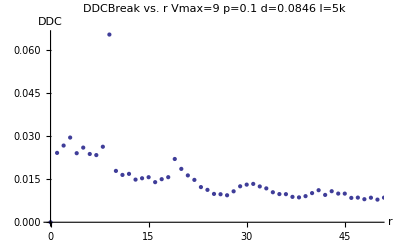

```mathematica
ddcb1=ddcb[[All,1]];
ddcb2=ddcb[[All,2]];
ListPlot[ddcb,PlotLabel->"DDCBreak vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,50},Full}]
```

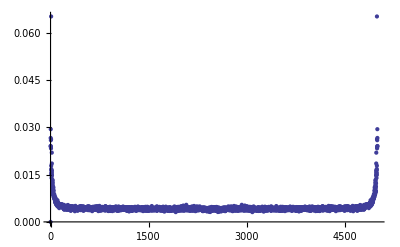

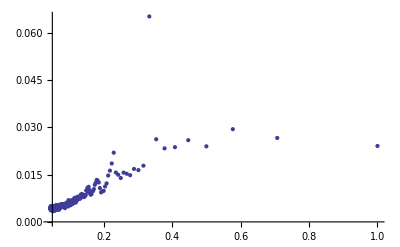

```mathematica
a=0.5;
data=Table[{1/ddcb1[[i]]^a,ddcb2[[i]]},{i,2,Length[ddcb]/10}];
ListPlot[ddcb,PlotRange->Full]
ListPlot[data,PlotRange->Full]
```

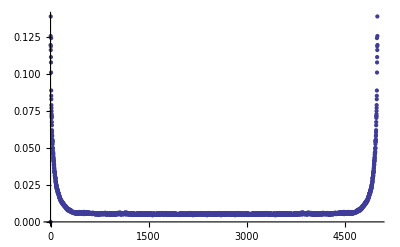

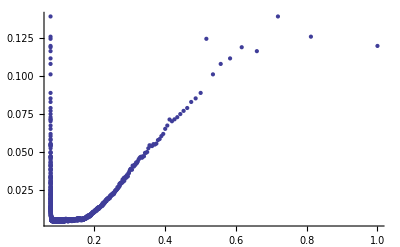

```mathematica
ListPlot[ddcb,PlotRange->Full]
ListPlot[data,PlotRange->Full]
```

```mathematica
ddcb[[2000]]
```

{1999,0.00538329}

-Graphics-

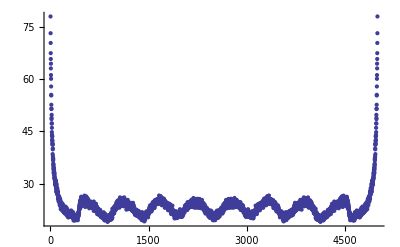

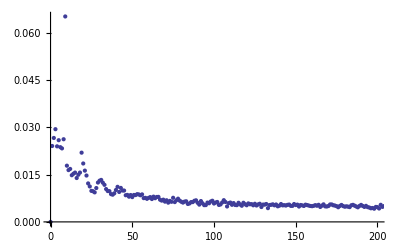

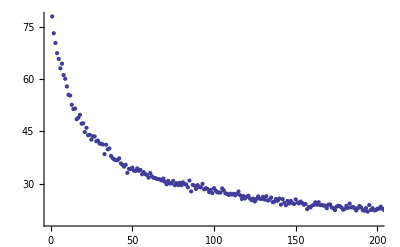

```mathematica
ListPlot[ddcb,PlotRange->Full]
ListPlot[fourierb,PlotRange->Full]
ListPlot[ddcb,PlotRange->{{0,200},Full}]
ListPlot[fourierb,PlotRange->{{0,200},Full}]
```

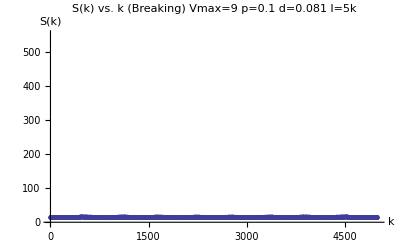

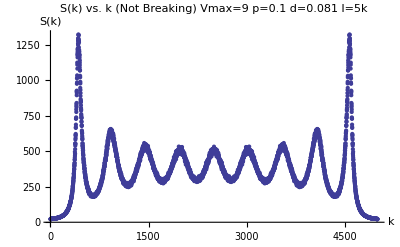

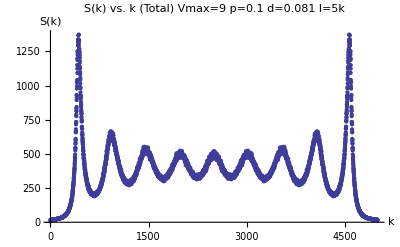

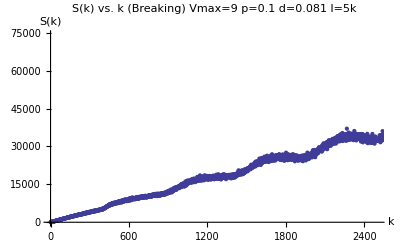

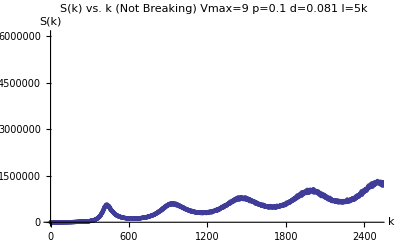

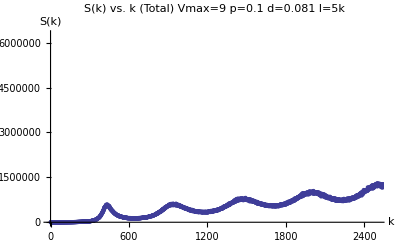

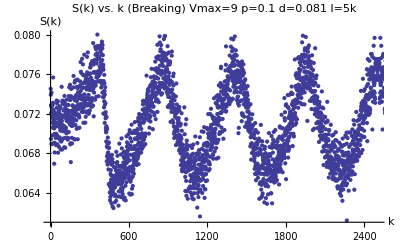

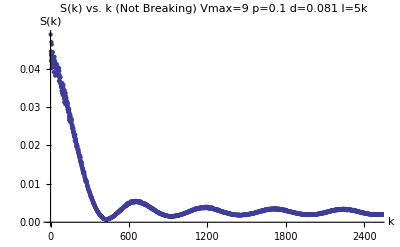

```mathematica
d="0.081";
l="5";
ll=5000;
v="9";
p="0.1";
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
fourierb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1DBreak-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
fourierf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1DFree-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];

fourierf2=Table[{fourierf[[All,1]][[i]],fourierf[[All,2]][[i]]*fourierf[[All,1]][[i]]},{i,1,Length[fourierf]}];
fourierb2=Table[{fourierb[[All,1]][[i]],fourierb[[All,2]][[i]]*fourierb[[All,1]][[i]]},{i,1,Length[fourierb]}];
fourier2=Table[{fourier[[All,1]][[i]],fourier[[All,2]][[i]]*fourier[[All,1]][[i]]},{i,1,Length[fourier]}];



fourierf3=Table[{fourierf[[All,1]][[i]],1/fourierf[[All,2]][[i]]},{i,1,Length[fourierf]}];
fourierb3=Table[{fourierb[[All,1]][[i]],1/fourierb[[All,2]][[i]]},{i,1,Length[fourierb]}];
fourier3=Table[{fourier[[All,1]][[i]],1/fourier[[All,2]][[i]]},{i,1,Length[fourier]}];


ListPlot[fourierb,PlotLabel->"S(k) vs. k (Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{Full,{0,550}}]

ListPlot[fourierf,PlotLabel->"S(k) vs. k (Not Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->Full]



ListPlot[fourier,PlotLabel->"S(k) vs. k (Total) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->Full]


ListPlot[fourierb2,PlotLabel->"S(k) vs. k (Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,ll/2},Full}]

ListPlot[fourierf2,PlotLabel->"S(k) vs. k (Not Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,ll/2},Full}]



ListPlot[fourier2,PlotLabel->"S(k) vs. k (Total) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,ll/2},Full}]

ListPlot[fourierb3,PlotLabel->"S(k) vs. k (Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,ll/2},Full}]

ListPlot[fourierf3,PlotLabel->"S(k) vs. k (Not Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,ll/2},Full}]



ListPlot[fourier3,PlotLabel->"S(k) vs. k (Total) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,ll/2},Full}]
```

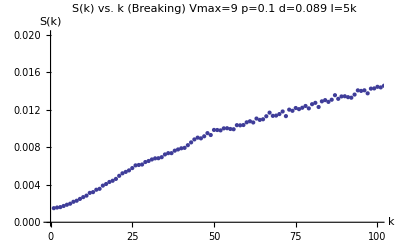

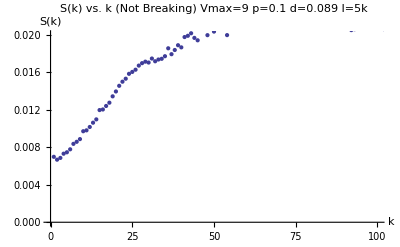

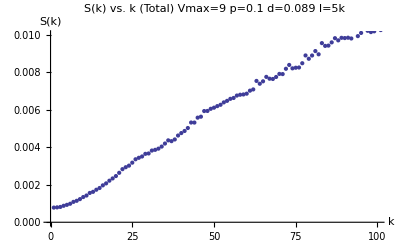

```mathematica
ListPlot[fourierb3,PlotLabel->"S(k) vs. k (Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,100},{0,0.02}}]

ListPlot[fourierf3,PlotLabel->"S(k) vs. k (Not Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,100},{0,0.02}}]



ListPlot[fourier3,PlotLabel->"S(k) vs. k (Total) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,100},{0,0.01}}]
```

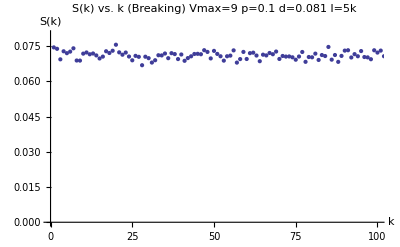

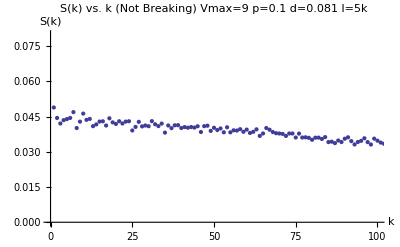

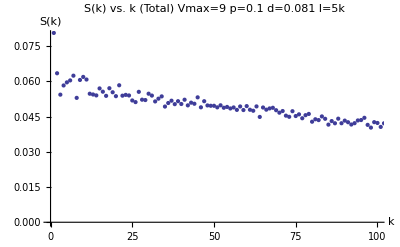

```mathematica
ListPlot[fourierb3,PlotLabel->"S(k) vs. k (Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,100},{0,0.08}}]

ListPlot[fourierf3,PlotLabel->"S(k) vs. k (Not Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,100},{0,0.08}}]



ListPlot[fourier3,PlotLabel->"S(k) vs. k (Total) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,100},{0,0.08}}]
```

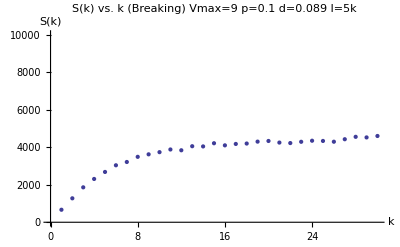

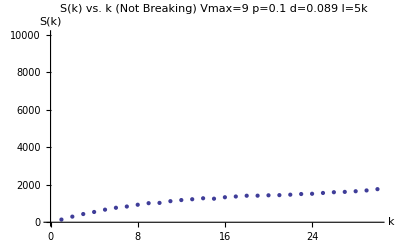

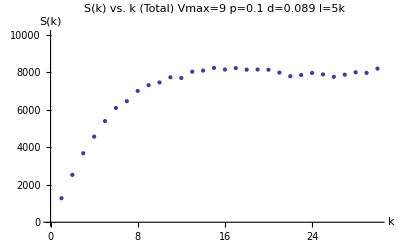

```mathematica
ListPlot[fourierb2,PlotLabel->"S(k) vs. k (Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,30},{0,10000}}]

ListPlot[fourierf2,PlotLabel->"S(k) vs. k (Not Breaking) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,30},{0,10000}}]



ListPlot[fourier2,PlotLabel->"S(k) vs. k (Total) Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k","S(k)"},PlotRange->{{0,30},{0,10000}}]
```